# Plot of Light Intensity with Interference of Two Coherent Light Sources

## Michelson Interferometer, Jan. 21 Using the relations and parameters as found in the Smetana article.

```mathematica
Clear["Global`*"]
```

```mathematica
omegap=Sqrt[(ne*(e^2))/(enot*me)]
e=1.6*10^-19
enot=8.854*10^-12
me=9.11*10^-31
```

√((e^2 ne)/(enot me))

1.6×10^-19

8.854×10^-12

9.11×10^-31

```mathematica
vlight=3*10^8
lambda=1064*10^-9
omega=(2*Pi*vlight)/lambda
indexref=1-0.5*((omegap^2)/omega)
```

300000000

133/125000000

(75000000000000000 π)/133

1-8.95762×10^-13 ne

```mathematica
armL1=2.5*10^8  (*Length of lisa's arm*)
armL2=(2.5*10^8)*indexref
opdiff=armL1-armL2 (*optical path difference*)
```

2.5×10^8

2.5×10^8 (1-8.95762×10^-13 ne)

2.5×10^8-2.5×10^8 (1-8.95762×10^-13 ne)

opdiff = need to find the relation with index of refraction and the difference in optical path-length difference. need not the individual lengths of the arms, only the difference in them. Thus, lambda can be used. 
Assuming that the arm length is changed by multiplying armL2 with the index of refraction. This leads to the optical path-length difference to be the difference between the length of the arm that is unchanging (armL1), and the length of the arm we assume will have a different length due t the introduction of electrons (armL2).

```mathematica
del=(opdiff/lambda)*2*Pi
Intens=(Cos[del/2])^(2)
```

250000000/133 (2.5×10^8-2.5×10^8 (1-8.95762×10^-13 ne)) π

Cos[125000000/133 (2.5×10^8-2.5×10^8 (1-8.95762×10^-13 ne)) π]^2

del comes from equation 1 from the resource sent by Dr. Holmstrom, http : // www.physnet.org/modules/pdf_modules/m205.pdf 
Intens is equation 4 in the same resource.

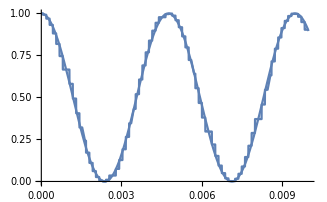

```mathematica
Intens=SetPrecision[Intens,20];
p1=Plot[Intens,{ne,0,0.01},WorkingPrecision->20];
p2=Plot[Intens,{ne,0,0.01}];
Show[p1,p2]
```

First attempt at plotting the intensity of the interference light as a function of the index of refraction of electrons (ne) as found in the Smetana article. The function Intens  only depends on the optical path-length-difference (opdiff), which again depends on ne. It does not take into consideration the coefficients, such as the constant of light intensity from the laser, and I believe there should be a factor of 2 multiplied as well. See equation 4 from: http://www.physnet.org/modules/pdf_modules/m205.pdf

I had to play around with the range of the plot to be able to see the wave, and I am not sure why it is not smooth, but has distinct “steps”. Maybe this is due to the parameters of the graph/function, or is there an optical reason why it looks like this?